```mathematica
basedir="D:\\data\\Cycle 194\\exp_CRG-3061\\rawdata\\sc\\"
Get[basedir<>"..\\camera_ifg.m"]
minIntens=2000;  (* Schwellenwert zur Unterdrückung schwach beleuchtetet Randbereiche der Kamera *)
(*
loadimage[basedir<>filename]    liefert Array mit den einzelnen Bildern aus der Tiff-Datei.;
fittile[images_,tileDX_,tileDY_,nx_,ny_,minIntensity_,period_]

*)
```

D:\data\Cycle 194\exp_CRG-3061\rawdata\sc\

```mathematica
reduceSlotsBy[img_,its_,slotmax_]:=Module[{maxph,maxtim},
maxtim=slotmax/its;
maxph=Length[img]/(slotmax+2);
Flatten[Table[    Join[{img[[1+(ph-1)*(slotmax+2)]]},Table[Total[img[[(ph-1)*(slotmax+2)+1+(tim-1)*its;;(ph-1)*(slotmax+2)+tim*its]],1],{tim,1,maxtim}],{img[[ph*(slotmax+2)]]}]     ,{ph,1,maxph}],1]
]
```

# Standard IFM

```mathematica
filename = "ifg_cam_24Oct1908.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
```

{31,50,40}

```mathematica
ArrayPlot[Reverse[img[[2]]],ColorFunction->GrayLevel]
```

-Graphics-

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

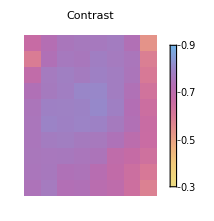
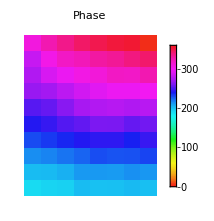
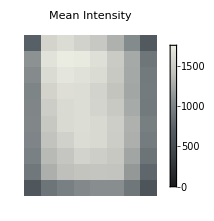
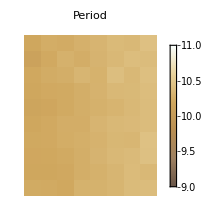

```mathematica
res=fitgrid[img,5,5,1,10];
plotres[res]
```

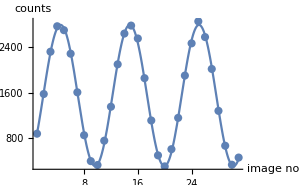
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 1549.72 | 6.93091 | 223.595 | 1.1671×10^-45
CameraIfgPackage`Private`b | 1248.44 | 9.73297 | 128.269 | 3.77659×10^-39
CameraIfgPackage`Private`c | 0.610132 | 0.000832944 | 732.5 | 1.43071×10^-59
CameraIfgPackage`Private`d | -1.1777 | 0.0144054 | -81.7542 | 6.99933×10^-34contr=0.80559
offs=1549.72
phase=292.523°
period=10.2981

```mathematica
showtileres[res,4,6]
```

```mathematica
filename = "ifg_cam_24Oct2156.tif";
```

{31,50,40}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

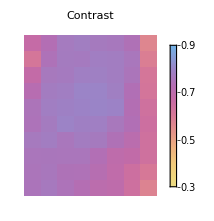
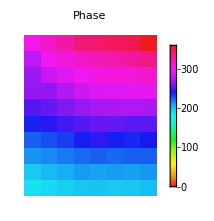
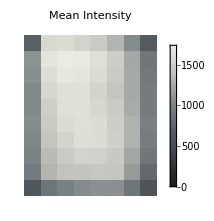
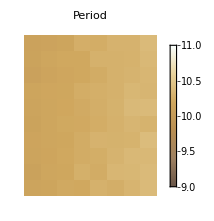

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
res=fitgrid[img,5,5,1,10];
plotres[res]
```

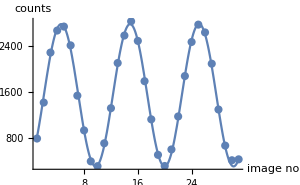
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 1550.21 | 9.71369 | 159.59 | 1.04347×10^-41
CameraIfgPackage`Private`b | 1237.7 | 13.6083 | 90.9517 | 3.97477×10^-35
CameraIfgPackage`Private`c | 0.61209 | 0.00118565 | 516.25 | 1.8107×10^-55
CameraIfgPackage`Private`d | -1.23636 | 0.0205886 | -60.0507 | 2.77608×10^-30contr=0.798409
offs=1550.21
phase=289.162°
period=10.2651

```mathematica
showtileres[res,4,6]
```

```mathematica
filename = "ifg_cam_25Oct0044.tif";
```

{31,50,40}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

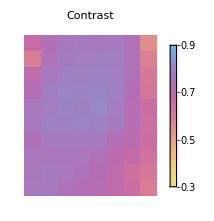
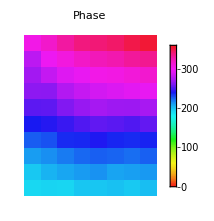
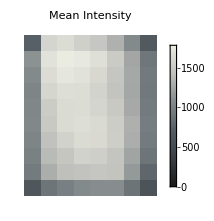
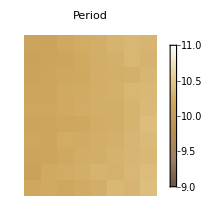

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
res=fitgrid[img,5,5,1,10];
plotres[res]
```

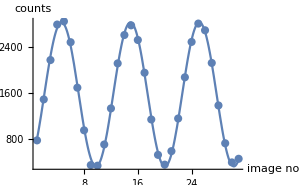
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 1574.82 | 8.62316 | 182.627 | 2.7468×10^-43
CameraIfgPackage`Private`b | 1263.08 | 12.0847 | 104.519 | 9.40502×10^-37
CameraIfgPackage`Private`c | 0.612611 | 0.00102863 | 595.561 | 3.82126×10^-57
CameraIfgPackage`Private`d | -1.27614 | 0.0178748 | -71.3937 | 2.67257×10^-32contr=0.802048
offs=1574.82
phase=286.882°
period=10.2564

```mathematica
showtileres[res,4,6]
```

```mathematica
filename = "ifg_cam_25Oct0332.tif";
```

{31,50,40}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

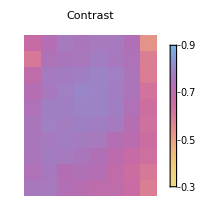
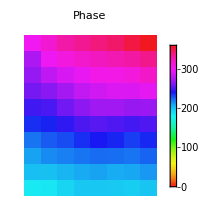
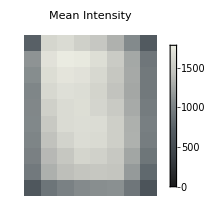
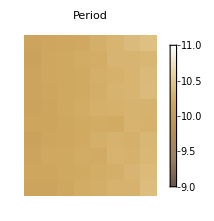

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
res=fitgrid[img,5,5,1,10];
plotres[res]
```

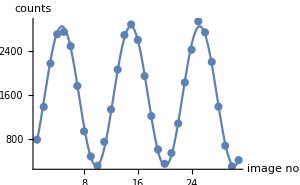
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 1580.47 | 10.7996 | 146.344 | 1.07987×10^-40
CameraIfgPackage`Private`b | 1258.68 | 15.1066 | 83.3199 | 4.20197×10^-34
CameraIfgPackage`Private`c | 0.612473 | 0.00130112 | 470.728 | 2.18858×10^-54
CameraIfgPackage`Private`d | -1.3049 | 0.0225836 | -57.781 | 7.79584×10^-30contr=0.7964
offs=1580.47
phase=285.234°
period=10.2587

```mathematica
showtileres[res,4,6]
```

```mathematica
filename = "ifg_cam_25Oct0619.tif";
```

{31,50,40}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

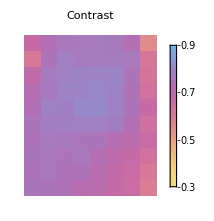
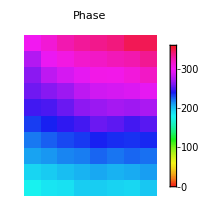
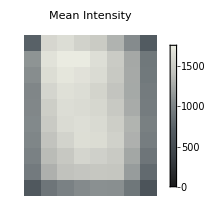
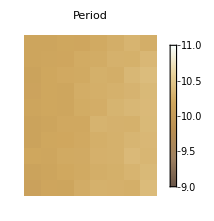

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
res=fitgrid[img,5,5,1,10];
plotres[res]
```

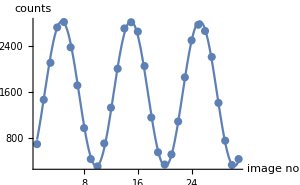
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 1564.1 | 10.3667 | 150.878 | 4.74286×10^-41
CameraIfgPackage`Private`b | 1257.18 | 14.5255 | 86.5499 | 1.51036×10^-34
CameraIfgPackage`Private`c | 0.611905 | 0.0012435 | 492.084 | 6.60623×10^-55
CameraIfgPackage`Private`d | -1.29765 | 0.0216451 | -59.9511 | 2.90245×10^-30contr=0.803771
offs=1564.1
phase=285.65°
period=10.2682

```mathematica
showtileres[res,4,6]
```

```mathematica
filename = "beampos_z9_y4.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
ArrayPlot[Reverse[binimage[img[[1]],5,5]],ColorFunction->GrayLevel,ImageSize->200,FrameTicks->True]
```

{1,50,40}

-Graphics-

```mathematica
filename = "beampos_z8_y4.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
ArrayPlot[Reverse[binimage[img[[1]],5,5]],ColorFunction->GrayLevel,ImageSize->200,FrameTicks->True]
```

{1,50,40}

-Graphics-

```mathematica
filename = "beampos_z7_y4.tif";
```

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
ArrayPlot[Reverse[binimage[img[[1]],5,5]],ColorFunction->GrayLevel,ImageSize->200,FrameTicks->True]
```

{1,50,40}

-Graphics-